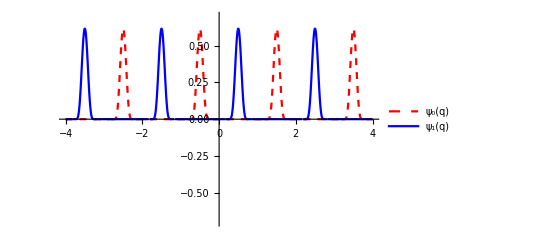

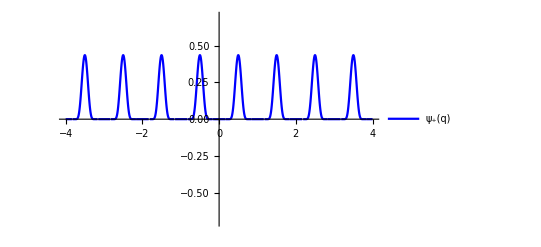

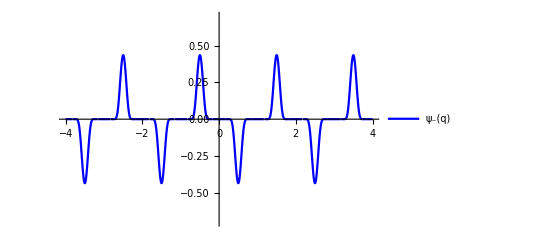

~/Documents/projectSiegen/firstDraft/plots/zeroOne.eps

~/Documents/projectSiegen/firstDraft/plots/plus.eps

~/Documents/projectSiegen/firstDraft/plots/minus.eps

```mathematica
L=1;
NN=4;
hbar=1;
phiP[x_]:=Exp[-1/((L/3)^2-(x^2))]HeavisideTheta[-Abs[x]+L/3] 5000
phi[x_] := phiP[x-L/2]
zeroP[x_]:=Sum[phi[x- (2 k  + 1)L],{k,-NN/2,NN/2 -1}]
oneP[x_] := Sum[phi[x-2k L],{k,-NN/2,NN/2 -1}]
plusP[x_]:=(oneP[x] + zeroP[x])/Sqrt[2]
minusP[x_]:=(zeroP[x] - oneP[x])/Sqrt[2]

p1=Plot[zeroP[x],{x,-4,4}, PlotRange->{-0.7,0.7}, PlotStyle->Dashed,PlotLegends->Placed[{"ψ_0(q)"},After]];
p0=Plot[oneP[x],{x,-4,4}, PlotRange->{-0.7,0.7},
PlotLegends->Placed[{"ψ_1(q)"},After]];

Show[p0,p1];
exp01=Plot[{zeroP[x],oneP[x]},{x,-4,4},PlotRange-> {-0.7,0.7},  PlotStyle->{{Dashed,Red},Blue},PlotLegends -> Placed[{"ψ_0(q)","ψ_1(q)"},After], BaseStyle->{FontSize->12}]

expP=Plot[plusP[x],{x,-4,4}, PlotRange->{-0.7,0.7},PlotStyle->Blue, PlotLegends -> Placed[{"ψ_+(q)"},After], BaseStyle->{FontSize->12}]

expM=Plot[minusP[x],{x,-4,4}, PlotRange->{-0.7,0.7},PlotStyle->Blue,PlotLegends -> Placed[{"ψ_-(q)"},After], BaseStyle->{FontSize->12}]
Export["~/Documents/projectSiegen/firstDraft/plots/zeroOne.eps",exp01]
Export["~/Documents/projectSiegen/firstDraft/plots/plus.eps",expP]
Export["~/Documents/projectSiegen/firstDraft/plots/minus.eps",expM]

psi[x_,y_]:=(plusP[x]minusP[y] - minusP[x]plusP[y])/Sqrt[2]
(*psi[a,b]*)
psiStar[x_,y_] :=Conjugate[psi[x,y]]
(*Plot3D[psi[x,y],{x,-10,10},{y,-10,10}]*)
(*wig[x_,px_,y_,py_]:=Integrate[Exp[ⅈ ((px qx) + (py qy))/hbar] psi[x - (1/2)qx,y-(1/2)qy] psiStar[x + (1/2)qx,y + (1/2)qy],{qx,-10,10},{qy,-10,10}]*)

(*wig[x_,px_,y_,py_] := FourierTransform[ psi[x - (1/2)qx, y - (1/2) qy] psiStar[x+(1/2)qx,y+(1/2)qy] ,{qx,qy},{px,py}]
wig[1,1,1,1]

Needs["FourierSeries`"]
f[t_]:=UnitStep[1-t] UnitStep[t+1]
ff[t_,k_] := UnitStep[1-t] UnitStep[t+1]UnitStep[1-k]UnitStep[k+1]
FourierTransform[ff[x,y],{x,y},{omega,omego}]
NFourierTransform[ff[x,y],{x,y},{1,2}]
NFourierTransform[f[x],x,1]
*)

(*f[t_]:=Sin[x]*)
(*g[omega_]:=FourierTransform[ f[x],x,omega]*)
(*Plot[g[omega],{omega,-10,10}]*)

(*Plot[NFourierTransform[ f[x],x,y],{y,-10,10},PlotRange->All]*)
(*Plot3D [wig[x,1,y,1],{x,-10,10},{y,-10,10}]*)
```

```mathematica
d=Real[d]
F=∑_(n=-1)^0 ∑_(m=-1)^0 (e^(ⅈ(n Subscript[p, 1]+m Subscript[p, 2])L)(Cos[d]((-1)^(m+1)-(-1)^(n+1))+ⅈ Sin[d](1+(-1)^(n+m+2))))
Conjugate[F]
Simplify[F ]
```

d∈Reals

-2 e^(-ⅈ L p_1) Cos[d]+2 e^(-ⅈ L p_2) Cos[d]+2 ⅈ Sin[d]+2 ⅈ e^(ⅈ L (-p_1-p_2)) Sin[d]

Conjugate::argx: Conjugate called with 2 arguments; 1 argument is expected.

Conjugate[-2 e^(-ⅈ L p_1) Cos[d]+2 e^(-ⅈ L p_2) Cos[d]+2 ⅈ Sin[d]+2 ⅈ e^(ⅈ L (-p_1-p_2)) Sin[d],d∈Reals]

(-2 e^(-ⅈ L p_1)+2 e^(-ⅈ L p_2)) Cos[d]+2 ⅈ (1+e^(-ⅈ L (p_1+p_2))) Sin[d]